```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mLC"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={010881,010959,010579,010575}];
Print["HV (: ",runHV={20,40,60,120}];
(*{010575=132kV,010579=60kV,010959=40kV,010881=20kV}
*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Word,Word,Word,Real,Real,Word,Word};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mLC

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10881,10959,10579,10575}

HV (: {20,40,60,120}

#Runs in the list: 4

```mathematica
datvi=Table[{},{k,1,runn}];datvi=Table[{},{k,1,runn}];
dimdatvi=Table[{},{k,1,runn}];
For[runi=1,runi≤4,runi++,
datvi[[runi]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_HV3.edm"],metaStructure];
Print["Size of V-I data file, run #",runNum[[runi]] ," = " ,dimdatvi=Dimensions[datvi[[runi]]][[1]]];
];
```

Size of V-I data file, run #10881 = 70747

Size of V-I data file, run #10959 = 51189

Size of V-I data file, run #10579 = 33422

Size of V-I data file, run #10575 = 77962

```mathematica
pt1=Rasterize[EDAListPlot[
Transpose[{datvi[[1]][[;;,4]],datvi[[1]][[;;,5]]}],Transpose[{datvi[[2]][[;;,4]],datvi[[2]][[;;,5]]}],Transpose[{datvi[[3]][[;;,4]],datvi[[3]][[;;,5]]}],
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},PlotLegends->{"V_max=20 kV","V_max=40 kV","V_max=66 kV","V_max=132 kV"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->Full,PlotLabel->"HV Power Supply: V vs. I",PlotMarkers->{Automatic,10}],
ImageResolution->100]
```

-Graphics-

## Steady State

```mathematica
vvalmax=0;del=0.1;vvalmin=0;minmaxr=110;
moddatvip=Table[{},{k,1,runn}];
moddatvin=Table[{},{k,1,runn}];
dimmoddatvip=Table[0,{k,1,runn}];
dimmoddatvin=Table[0,{k,1,runn}];
vi=Table[{0,{0,0}},{k,1,2runn}];
For[i=1,i≤runn,i++,
Print["Run #",runNum[[i]]," {Max,Min}: { ",vvalmax=RankedMax[datvi[[i]][[;;,4]],minmaxr ]," , ",vvalmin=RankedMin[datvi[[i]][[;;,4]],minmaxr ]," }"];
moddatvip[[i]]=Select[datvi[[i]],(#[[4]]==vvalmax)&];
Print["Size of V-I data file, + run #",runNum[[i]] ," = " ,dimmoddatvip[[i]]=Dimensions[moddatvip[[i]]][[1]]];
vi[[i]]={Mean[moddatvip[[i]][[;;,4]]],{Mean[Abs[moddatvip[[i]][[;;,5]]]].1,StandardDeviation[Abs[moddatvip[[i]][[15;;110,5]]]].1}};
moddatvin[[i]]=Select[datvi[[i]],(#[[4]]==vvalmin)&];(*((#[[4]]>vvalmin)&&(#[[4]]<vvalmin+del))&*)
Print["Size of V-I data file, - run #",runNum[[i]] ," = " ,dimmoddatvin[[i]]=Dimensions[moddatvin[[i]]][[1]]];
vi[[4+i]]={Mean[moddatvin[[i]][[;;,4]]],{-Mean[Abs[moddatvin[[i]][[;;,5]]]].1,StandardDeviation[Abs[moddatvin[[i]][[15;;110,5]]]].1}};
];
vi
Print["Resistance, R (GΩ)= ",vi[[1]][[1]]/vi[[1]][[2]][[1]]," ± ",vi[[1]][[1]]/vi[[1]][[2]][[1]]/(vi[[1]][[2]][[1]]/vi[[1]][[2]][[2]])];
pt1=EDAListPlot[vi,
PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"R = (6.0 ± 1.3)TΩ",PlotMarkers->{Automatic,10}];
pt2=Plot[{.00012x,.00012x+RootMeanSquare[vi[[;;,2]][[;;,2]]],.00012x-RootMeanSquare[vi[[;;,2]][[;;,2]]]},{x,-135,135},Filling->{2->{3}},
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"R = (6.0 ± 1.3)TΩ"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
```

Run #10881 {Max,Min}: { 20.004 , -19.997 }

Size of V-I data file, + run #10881 = 735

Size of V-I data file, - run #10881 = 113

Run #10959 {Max,Min}: { 39.999 , -39.999 }

Size of V-I data file, + run #10959 = 13014

Size of V-I data file, - run #10959 = 4666

Run #10579 {Max,Min}: { 66.002 , -65.992 }

Size of V-I data file, + run #10579 = 2619

Size of V-I data file, - run #10579 = 5261

Run #10575 {Max,Min}: { 131.995 , -131.99 }

Size of V-I data file, + run #10575 = 4272

Size of V-I data file, - run #10575 = 3110

{{20.004,{0.00335252,0.000718231}},{39.999,{0.00335305,0.00134146}},{66.002,{0.0126156,0.00570833}},{131.995,{0.0149831,0.00194232}},{-19.997,{-0.00209027,0.000759997}},{-39.999,{-0.00304944,0.00131827}},{-65.992,{-0.00973515,0.00255279}},{-131.99,{-0.0171654,0.00545245}}}

Resistance, R (GΩ)= 5966.86 ± 1278.32

-Graphics-

```mathematica
RootMeanSquare[vi[[;;,2]][[;;,2]]]
```

0.00310714

```mathematica
rr=6×10^12;
Print["Capacitance of chamber : ", cc=8.5*10^-12*Pi*.23^2/.12];
pt1=EDAListPlot[
Transpose[{datvi[[1]][[;;,4]],datvi[[1]][[;;,5]]}],
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->Full,PlotLabel->"R = 6.0 TΩ , C = 11.8 pF",PlotMarkers->{Automatic,10}];
pt2=Plot[{.89ArcTan[10xx]+.005xx-.00005xx^2,
.89ArcTan[10xx]+.005xx-.00005xx^2+.1,
.89ArcTan[10xx]+.005xx-.00005xx^2-.1,
ConditionalExpression[.9ArcTan[10(xx-20)]+.004(xx-20)+.00005(xx-20)^2,xx>0],
ConditionalExpression[.9ArcTan[10(xx-20)]+.004(xx-20)+.00005(xx-20)^2+.1,xx>0],
ConditionalExpression[.9ArcTan[10(xx-20)]+.004(xx-20)+.00005(xx-20)^2-.1,xx>0],
.89ArcTan[10(xx+20)]+.005(xx+20.5)-.00005(xx+20)^2,
.89ArcTan[10(xx+20)]+.005(xx+20.5)-.00005(xx+20)^2+.1,
.89ArcTan[10(xx+20)]+.005(xx+20.5)-.00005(xx+20)^2-.1},
{xx,-25,25},
Filling->{{2->{3}},{5->{6}},{8->{9}}},PlotStyle->{{Red,Thick},{Red,Thin},{Red,Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Red,Thick},{Red,Thin},{Red,Thin}},
Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->Full,PlotLabel->"R = 6.0 TΩ , C = 11.8 pC"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
(*pt2=Plot[{1.5(1-Exp[-500xx/(rr cc)]-.0005xx^2+.015xx-.1),.9ArcTan[10xx]+.005xx+.1},{xx,-25,25},PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->Full,PlotLabel->"HV Power Supply: V vs. I"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]*)
```

Capacitance of chamber : 1.17718×10^-11

-Graphics-

```mathematica
runNum2={12302,12304,12305};
Print["#Runs in the list: ",runn2=Dimensions[runNum2][[1]]];
datvi2=Table[{},{k,1,runn2}];
vi2=Table[Table[{0,{0,0}},{k,1,14}],{k,1,runn2}];
dimdatvi2=Table[0,{k,1,runn2}];
For[runi=1,runi≤runn2,runi++,
datvi2[[runi]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[runi]],10,6],"\\",IntegerString[runNum2[[runi]],10,6],"_HV32.edm"],metaStructure];
Print["Size of V-I data file, run #",runNum2[[runi]] ," = " ,dimdatvi2[[runi]]=Dimensions[datvi2[[runi]]][[1]]];
];
(*4:V, 5:I*)
```

#Runs in the list: 3

Size of V-I data file, run #12302 = 53870

Size of V-I data file, run #12304 = 48499

Size of V-I data file, run #12305 = 44632

```mathematica
(*12302*)
del=.1;
maxv=100;
maxc=10;
vi12302=Table[{0,{0,0}},{k,1,11}];
For[i=0,i≤2maxc,i+=2,
ival=Select[datvi2[[1]],(#[[4]]>(10*i-maxv-del))&][[;;,5]];
vi12302[[Round[i/2]+1]]={i*10-maxv,{Mean[ival]/3.25-.015,StandardDeviation[ival]/100}};
];
RootMeanSquare[vi12302[[;;,2]][[;;,2]]]
pt1=EDAListPlot[vi12302,
PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12302, R = 6.0 TΩ",PlotMarkers->{Automatic,10}];
pt2=Plot[{.00012x,.00012x+RootMeanSquare[vi[[;;,2]][[;;,2]]],.00012x-RootMeanSquare[vi[[;;,2]][[;;,2]]]},{x,-135,135},Filling->{2->{3}},
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12302, R = 6.0 TΩ"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
```

0.00210465

-Graphics-

```mathematica
(*12304*)
del=.1;
maxv=80;
maxc=Round[maxv/10];
vi12304=Table[{0,{0,0}},{k,1,maxc+1}];
For[i=0,i≤2maxc,i+=2,
ival=Select[datvi2[[2]],(#[[4]]>(10*i-maxv-del))&][[;;,5]];
vi12304[[Round[i/2]+1]]={i*10-maxv,{Mean[ival]/3.5-.01,StandardDeviation[ival]/100}};
];
vi12304
RootMeanSquare[vi12304[[;;,2]][[;;,2]]]
pt1=EDAListPlot[vi12302,vi12304,
PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},PlotLegends->{"12302", "12304"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12304, R = 6.0 TΩ",PlotMarkers->{Automatic,20}];
pt2=Plot[{.00012x,.00012x+RootMeanSquare[vi[[;;,2]][[;;,2]]],.00012x-RootMeanSquare[vi[[;;,2]][[;;,2]]]},{x,-135,135},Filling->{2->{3}},
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12304, R = 6.0 TΩ"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
```

{{-80,{-0.00910046,0.00122363}},{-60,{-0.0069011,0.00119272}},{-40,{-0.00482275,0.00116074}},{-20,{-0.00284405,0.00112582}},{0,{-0.00099998,0.00108287}},{20,{0.00298409,0.00113529}},{40,{0.0054512,0.00106818}},{60,{0.00796878,0.000930285}},{80,{0.0105425,0.0000539787}}}

0.00105438

-Graphics-

```mathematica
(*12304*)
del=.1;
maxv=140;
maxc=Round[maxv/10];
vi12305=Table[{0,{0,0}},{k,1,maxc+1}];
For[i=0,i≤2maxc,i+=2,
ival=Select[datvi2[[3]],(#[[4]]>(10*i-maxv-del))&][[;;,5]];
vi12305[[Round[i/2]+1]]={i*10-maxv,{Mean[ival]/3.5-.0225,StandardDeviation[ival]/100}};
];
vi12305
RootMeanSquare[vi12305[[;;,2]][[;;,2]]]
pt1=EDAListPlot[vi12302,vi12304,vi12305,
PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},PlotLegends->{"12302", "12304","12305"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12305, R = 6.0 TΩ",PlotMarkers->{Automatic,20}];
pt2=Plot[{.00012x,.00012x+RootMeanSquare[vi[[;;,2]][[;;,2]]],.00012x-RootMeanSquare[vi[[;;,2]][[;;,2]]]},{x,-135,135},Filling->{2->{3}},
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12304, R = 6.0 TΩ"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
```

{{-140,{-0.0208665,0.00345127}},{-120,{-0.0157194,0.00275862}},{-100,{-0.0106858,0.00279679}},{-80,{-0.0108567,0.00269342}},{-60,{-0.00601512,0.00274198}},{-40,{-0.00622139,0.0026148}},{-20,{-0.00124656,0.00270226}},{0,{-0.00119732,0.00257569}},{20,{0.0037493,0.00269449}},{40,{0.00378766,0.00253872}},{60,{0.00894069,0.00270117}},{80,{0.00891862,0.00248827}},{100,{0.0140067,0.00272697}},{120,{0.0139212,0.00240134}},{140,{0.0165557,0.000224541}}}

0.00262471

-Graphics-

```mathematica
pt1=EDAListPlot[vi12302,vi12304,vi12305,vi,
PlotStyle->{Red,Thick},Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},PlotLegends->{"12302", "12304","12305","{010881,\n010959,\n010579,\n010575}"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12305, R = 6.0 TΩ",PlotMarkers->{Automatic,20}];
pt2=Plot[{.00012x,.00012x+RootMeanSquare[vi[[;;,2]][[;;,2]]],.00012x-RootMeanSquare[vi[[;;,2]][[;;,2]]]},{x,-135,135},Filling->{2->{3}},
PlotStyle->Thick,Frame->True,FrameTicks->LinTicks,FrameLabel->{"V (kV)","I (μA)"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,PlotRange->{{-135,135},{-.025,.025}},PlotLabel->"Run #12304, R = 6.0 TΩ"];
Rasterize[Show[{pt1,pt2}],ImageResolution->100]
```

-Graphics-

## 12302(20,40,60,80,100)

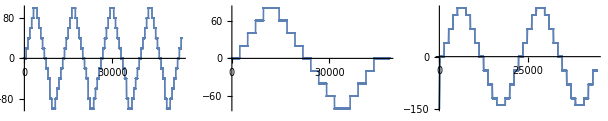

```mathematica
GraphicsGrid[{{ListPlot[datvi2[[1]][[;;,4]],PlotRange->Full],ListPlot[datvi2[[2]][[;;,4]],PlotRange->Full],ListPlot[datvi2[[3]][[;;,4]],PlotRange->Full]}}]
```